# Random graph generation

Understanding the processes of network formation.

Máté Csigi, Jun. 24,  2018

One of the most fascinating results of network science is that networks taken from entirely different domains are remarkably similar to each other in many respect. Understanding the processes responsible for these similarities is one of the primary motivations behind developing graph generating models.

## Generating a graph

One of the most known models for generating random graphs is based on the concept of preferential attachment which means that new nodes are more likely to connect to well-connected elements of the network. So nodes with many connections are likely to get even more links. Here is a graph generated with the preferential attachment model:

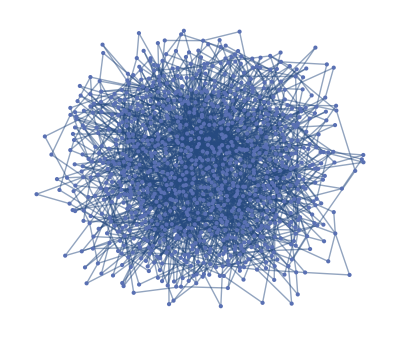

```mathematica
graph=RandomGraph[BarabasiAlbertGraphDistribution[1000,2]]
```

## Degree distribution

One of the similarities that all kinds of real-world networks share is that their degree distribution follows a power law. For this reason these networks are usually called scale-free. The graphs generated by the Barabasi model are scale-free as well:

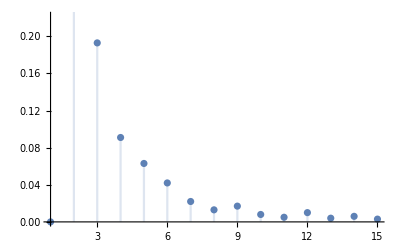

```mathematica
degrees=EmpiricalDistribution[VertexDegree[graph]];
DiscretePlot[PDF[degrees,k],{k,1,15}]
```

## Diameter scaling

Another property that real networks have in common is their really small diameter which means that any node can be reached in only a very few steps from any part of the network. The diameter and the average path length of the networks scale with the logarithm of the network size as plotted in the figure below:

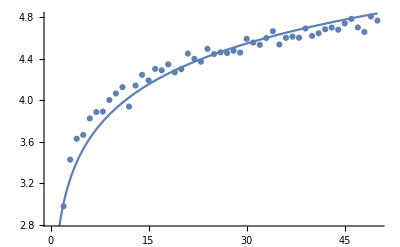

```mathematica
diameters=Table[MeanGraphDistance[RandomGraph[BarabasiAlbertGraphDistribution[n,2]]],{n,10,5000,100}];
fitDiam=Fit[diameters,{1,Log[x]},x];
Show[ListPlot[diameters],Plot[fitDiam,{x,0,50}]]
```

## Clusters

Nodes in real-world networks tend to form very tightly connected clusters that in many cases represents the separation of functional roles as well e.g. in protein interaction networks. The grouping of nodes into middle-sized clusters can be clearly observed on our generated network:

```mathematica
CommunityGraphPlot[graph]
```

-Graphics-

## Rich-club distribution

Despite all these similarities , however, there are some network measures that are very different for networks from different domains. The most notable of these is the rich-club distribution that quantifies how much the most influential nodes are connected to each other. For calculating the rich-club distribution the subgraphs containing only the nodes with more than a given number of links are investigated. Such subgraphs are plotted in the following figure:

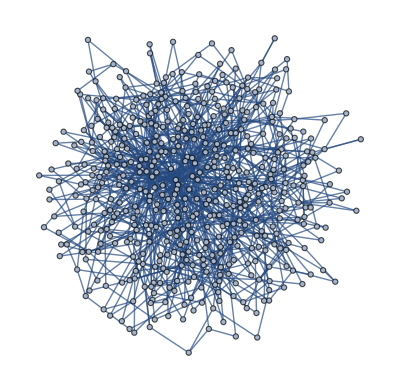
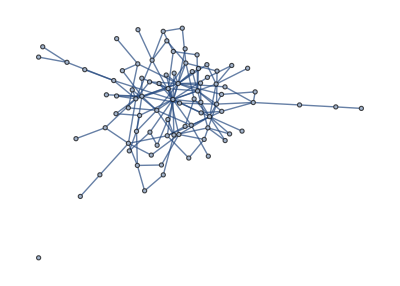
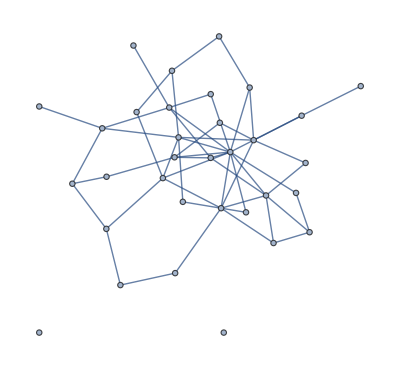
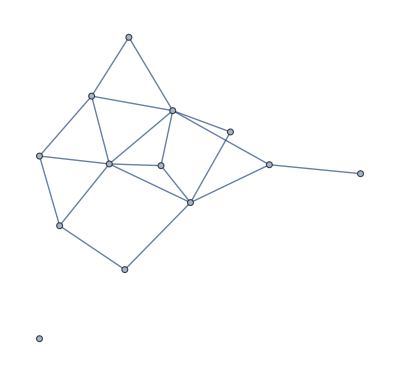

```mathematica
Table[Subgraph[graph,Select[VertexList[graph],VertexDegree[graph,#]>k&]],{k,2,18,5}]
```

The rich-club distribution is calculated by counting the edges in the subgraphs and after normalizing with the number of all possible connections within the given subgraph:

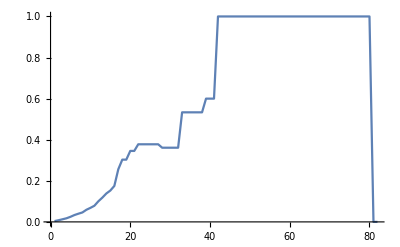

```mathematica
RichClub[g_Graph]:=Table[sub=Subgraph[graph,Select[VertexList[graph],VertexDegree[graph,#]>k&]];2 EdgeCount[sub]/Max[{1,(VertexCount[sub] (VertexCount[sub]-1))}],{k,1,Max[VertexDegree[graph]]}];
ListLinePlot[RichClub[graph]]
```

## Author contact information

csimate5@gmail.com